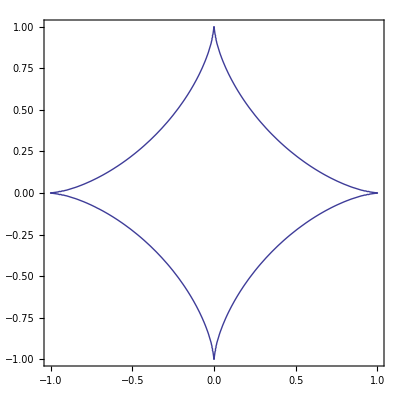

```mathematica
G=ContourPlot[CubeRoot[x^2]+CubeRoot[y^2]==1,{x,-1,1},{y,-1,1}]
```

```mathematica
(*Вычислим площадь астроиды, используя метод Монте-Карло*)
(*Зададим количество точек*)
n=10000;
(*Зададим равномерное распределение точек внутри квадрата [-1;1]x[-1;1]*)
Points=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{i,1,n}];
(*Найдем количество точек, принадлежащих астроиде*)
k=0;
For[i=1,i≤n,i++,
If[CubeRoot[Points[[i,1]]^2]+CubeRoot[Points[[i,2]]^2]≤1,k=k+1]
]
(*Найдем площадь астроиды*)
S=k/n*4;
Print["Площадь астроиды равна: ",N[S]]
(*Найдем точное значение площади астроиды*)
Exact=4*Integrate[Sqrt[(1-CubeRoot[x^2])^3],{x,0,1}];
Print["Точное значение площади астроиды равно: ",Exact]
Print["Погрешность равна: ",N[Abs[S-Exact]]]
```

Площадь астроиды равна: 1.1532

Точное значение площади астроиды равно: (3 π)/8

Погрешность равна: 0.0248972

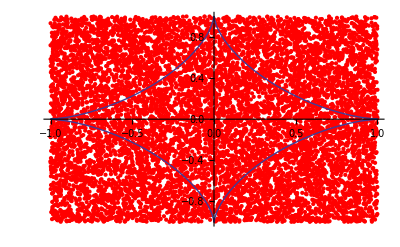

```mathematica
Show[ListPlot[Points,PlotStyle->Red],G]
```

```mathematica
Animate[Show[G,ListPlot[{Points[[i]]},PlotStyle->Red]],{i,1,n,1},AnimationRunning->False]
```